# Throwing Dice

In this notebook, we'll simulate the rolling of dice.

## Clear symbols

In order to avoid interference from symbols defined in other notebooks, we first Clear and Remove all symbols.  We assume that the relevant symbols are in the Global` context.

```mathematica
Clear["Global`*"]
```

```mathematica
Remove["Global`*"]
```

## Load some useful packages

If you are using a Mathematica version 6 or earlier, you will need to "uncomment" the following line (which means removing "(*" and "*)".  These functions are now built-in from version 7 on.

```mathematica
(*  <<"BarCharts`";<<"Histograms`"; *)
```

## Simulate the dice!

Possible outcomes of throwing a single die:

```mathematica
dots = {1,2,3,4,5,6}
```

{1,2,3,4,5,6}

We define a uniform probability distribution for the results 1 to 6, and call it "dice":

```mathematica
dice ={1,6};
```

How many times we toss the die => trials:

```mathematica
trials = 120;
```

Toss it (suppressing output with a ; when trials is large):

```mathematica
toss = RandomInteger[dice,trials];
```

```mathematica
?RandomInteger
```

RowBox[{"RandomInteger", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}], "]"}] gives a pseudorandom integer in the range RowBox[{"{", RowBox[{SubscriptBox["i", "min"], ",", "…", ",", SubscriptBox["i", "max"]}], "}"}]. 
RowBox[{"RandomInteger", "[", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]], "]"}] gives a pseudorandom integer in the range RowBox[{"{", RowBox[{"0", ",", "…", ",", SubscriptBox["i", "max"]}], "}"}]. 
RowBox[{"RandomInteger", "[", "]"}] pseudorandomly gives 0 or 1. 
RowBox[{"RandomInteger", "[", RowBox[{StyleBox["range", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives a list of StyleBox["n", "TI"] pseudorandom integers. 
RowBox[{"RandomInteger", "[", RowBox[{StyleBox["range", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] gives an RowBox[{SubscriptBox["n", "1"], "×", SubscriptBox["n", "2"], "×", "…", " "}] array of pseudorandom integers. 
RowBox[{"RandomInteger", "[", RowBox[{StyleBox["dist", "TI"], ",", StyleBox["…", "TR"]}], "]"}] samples from the symbolic discrete distribution StyleBox["dist", "TI"].

Count how many of each number (between 1/2 and 3/2, 3/2 and 5/2, etc):

```mathematica
freq = BinCounts[toss,{.5,6.5,1}]
```

{19,16,21,31,9,24}

```mathematica
?BinCounts
```

RowBox[{"BinCounts", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] counts the number of elements SubscriptBox[StyleBox["x", "TI"], StyleBox["i", "TI"]] whose values lie in successive integer bins.
RowBox[{"BinCounts", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["dx", "TI"]}], "]"}] counts the number of elements SubscriptBox[StyleBox["x", "TI"], StyleBox["i", "TI"]] whose values lie in successive bins of width StyleBox["dx", "TI"].
RowBox[{"BinCounts", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]], ",", StyleBox["dx", "TI"]}], "}"}]}], "]"}] counts the number of SubscriptBox[StyleBox["x", "TI"], StyleBox["i", "TI"]] in successive bins of width StyleBox["dx", "TI"] from SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]] to SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"BinCounts", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["b", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["b", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "}"}]}], "]"}] counts the number of SubscriptBox[StyleBox["x", "TI"], StyleBox["i", "TI"]] in the intervals RowBox[{RowBox[{"[", RowBox[{SubscriptBox[StyleBox["b", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["b", "TI"], StyleBox["2", "TR"]]}]}], ")"}], RowBox[{RowBox[{"[", RowBox[{SubscriptBox[StyleBox["b", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["b", "TI"], StyleBox["3", "TR"]]}]}], ")"}], StyleBox["…", "TR"]. 
RowBox[{"BinCounts", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["xbins", "TI"], ",", StyleBox["ybins", "TI"], ",", StyleBox["…", "TR"]}], "]"}] gives an array of counts where the first index corresponds to StyleBox["x", "TI"] bins, the second to StyleBox["y", "TI"], and so on.

Plot the frequency of each result as a histogram:

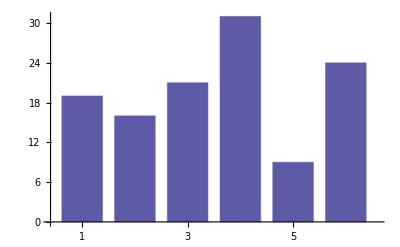

```mathematica
BarChart[freq]
```

Efficient way to add up the elements of the list "dots" ==>  Apply the "Plus" operator to each element:

```mathematica
Plus @@ dots
```

21

Calculate the average value of the number of dots:

```mathematica
N[ Plus @@ (freq*dots) / trials ]
```

3.55833

Calculate the average value of the number of dots squared:

```mathematica
N[ Plus @@ (freq*dots^2) / trials ]
```

15.475

Let's define a function that combines all of these steps:

```mathematica
Rolldice[trials_] := (
dots = {1,2,3,4,5,6};
dice ={1,6};
toss = RandomInteger[dice,trials];
freq=BinCounts[toss,{.5,6.5,1}];
avgdots = N[Plus@@(freq*dots)/trials];
avgdotssq = N[Plus@@(freq*dots^2)/trials];
sdev = Sqrt[avgdotssq-avgdots^2];
Print["mean = ",avgdots,"  standard deviation = ",sdev];
BarChart[freq] )
```

mean = 3.75  standard deviation = 1.78536

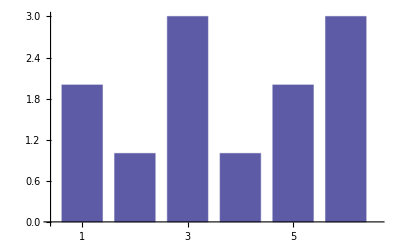

```mathematica
Rolldice[12]
```

mean = 3.4  standard deviation = 1.5885

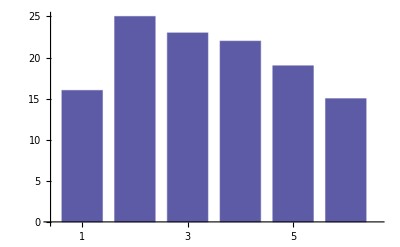

```mathematica
Rolldice[120]
```

mean = 3.605  standard deviation = 1.7221

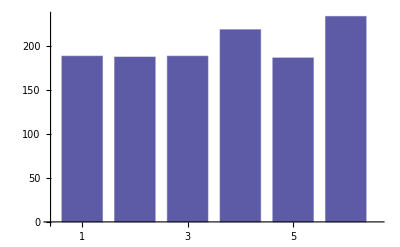

```mathematica
Rolldice[1200]
```

mean = 3.51008  standard deviation = 1.72194

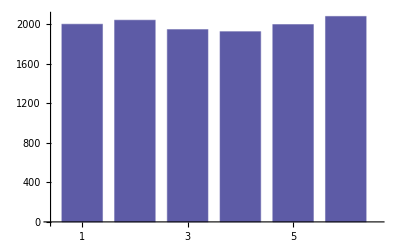

```mathematica
Rolldice[12000]
```

mean = 3.50522  standard deviation = 1.7079

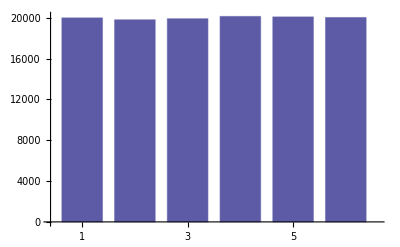

```mathematica
Rolldice[120000]
```

mean = 3.49961  standard deviation = 1.70766

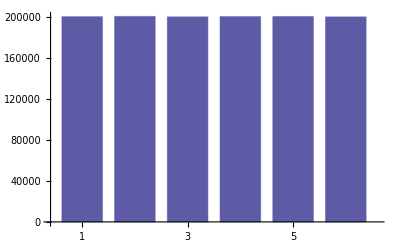

```mathematica
Rolldice[1200000]
```